```mathematica
lp[f_,x_,a_,b_,n_]:=Module[{},
h=(b-a)/n//N;
s=0;
Do[
s=s+h*(f/.x->(a+i*h)),
{i,0,n-1}];
s
]
```

```mathematica
f[x_]=E^(-x^2);
```

```mathematica
lp[f[x],x,0,1,100]
```

0.749979

```mathematica
dp[f_,x_,a_,b_,n_]:=Module[{},
h=(b-a)/n//N;
s=0;
Do[
s=s+h*(f/.x->(a+i*h)),
{i,1,n}];
s
]
```

```mathematica
sp[f_,x_,a_,b_,n_]:=Module[{},
h=(b-a)/n//N;
s=0;
Do[
s=s+h*(f/.x->(a+(i+1/2)h)),
{i,0,n-1}];
s
]
```

```mathematica
sp[f[x],x,0,1,100]
```

0.746827

```mathematica
f[x_]=E^(-x^2);
```

```mathematica
a=0;b=1;
```

```mathematica
prvi[x_]=D[f[x],x]
```

-2 ⅇ^(-x^2) x

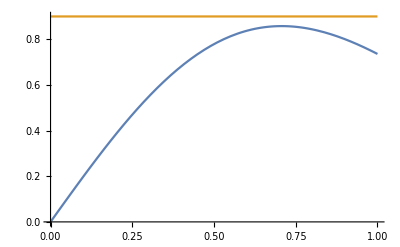

```mathematica
Plot[{Abs[prvi[x]],0.9},{x,0,1}]
```

```mathematica
m1=0.9;
```

```mathematica
greska=(b-a)/2 m1*(b-a)/n
```

0.45/n

```mathematica
Solve[greska==10^-4,n]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n→4500.}}

```mathematica
h=(b-a)/n
```

1/4500

```mathematica
n=4500;
```

```mathematica
h*Sum[f[a+i*h],{i,0,n-1}]//N
```

0.746894

```mathematica
f[x_]=E^(-x^2)
```

ⅇ^(-x^2)

```mathematica
a=0;b=1;n=10;
h=(b-a)/n//N;
```

```mathematica
h/2(f[a]+2*Sum[f[a+i*h],{i,1,n-1}]+f[b])
```

0.746211

```mathematica
drugi[x_]=D[f[x],{x,2}]
```

-2 ⅇ^(-x^2)+4 ⅇ^(-x^2) x^2

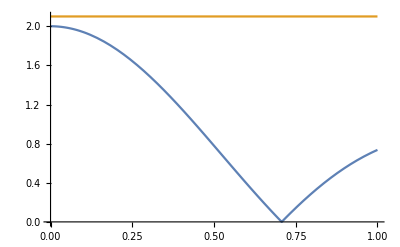

```mathematica
Plot[{Abs[drugi[x]],2.1},{x,0,1}]
```

```mathematica
m2=2.1
```

2.1

```mathematica
greska=(b-a)/12 m2*h^2
```

0.00175